# Let' s get electric

## functions

### options settings

```mathematica
SetDirectory["/home/julian/mathematica/CVL-electron"];
ClearSystemCache[];
Needs["Splines`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
SetOptions[Interpolation, InterpolationOrder -> 4, PeriodicInterpolation -> True];
Options[Interpolation]
```

{InterpolationOrder→4,PeriodicInterpolation→True}

```mathematica
SetOptions[NIntegrate, MaxRecursion -> 20];
Options[NIntegrate, MaxRecursion]
```

{MaxRecursion→20}

```mathematica
SetOptions[NDSolve`FiniteDifferenceDerivative, DifferenceOrder -> 6, PeriodicInterpolation -> True];
Options[NDSolve`FiniteDifferenceDerivative]
```

{DifferenceOrder→6,PeriodicInterpolation→True}

```mathematica
SetOptions[NDSolve, MaxSteps -> 15000];
Options[NDSolve, {MaxSteps, InterpolationOrder}]
```

{MaxSteps→15000,InterpolationOrder→Automatic}

```mathematica
SetOptions[NDSolve`ProcessEquations, MaxSteps -> 15000];
Options[NDSolve`ProcessEquations, MaxSteps]
```

{MaxSteps→15000}

### curve generator

```mathematica
Clear[curgen];

curgen[num_,xy__List,isx_:nan]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,ustart1,ustart2,u1,u2,initialarea,add,length,centroid},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

length = NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]], {u, 0,2 π}];centroid = 1/length NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]], {u, 0,2 π}, AccuracyGoal -> 9];

If[
!NumberQ[isx],
ustart1=0;ustart2=π;,
ustart1=u/.FindRoot[initialcurve[u][[1]]==isx,{u,π}];
ustart2=u/.FindRoot[initialcurve[u][[1]]==isx,{u,0}];
];

initialarea=Block[{a1,a2},
{u1,u2}={u,p}/.FindRoot[{initialcurve[u]==initialcurve[p]},{{u,ustart1},{p,ustart2}},MaxIterations->200];

a1=1/2NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,u1,u2},AccuracyGoal->10];
a2=1/2NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,u2,2π+u1},AccuracyGoal->10];

(*{u1,u2,a1,a2,Abs[a1]+Abs[a2],Abs[Abs[a1]-Abs[a2]]}*)
Abs[a1]+Abs[a2]
];

Subscript[curve, num][u_]:=Sqrt[100 2π/initialarea] (initialcurve[u]-centroid);

Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ParametricPlot[initialcurve[u],{u,0,2Pi},Epilog->{Green,PointSize[Medium],Opacity[.5],Point[{initialcurve[u1],initialcurve[u2]}]}],
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}],PlotStyle->{Black}]],
Show[
ParametricPlot[Subscript[curve, num][u],{u,0,2Pi},ColorFunction->Function[{x,y,u},Hue[u]]],
ListPlot[Table[100 4π/initialarea(xy[[i]]-centroid),{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num][2Pi i/100],{i,0,100}],PlotStyle->{Black},AspectRatio->Full]
]
}}]
];

{Subscript[A0, num]=diffA[num],length,centroid}

]
```

### continuous: area difference, length

```mathematica
Clear[diffA,iniL,iniA];

diffA[num_]:=1/2NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,0,2π},AccuracyGoal->8];

iniL[num_]:=NIntegrate[Sqrt[Evaluate[(D[Subscript[curve, num][u], u]).(D[Subscript[curve, num][u], u])]], {u, 0,2 π}];

iniA[num_]:=
Module[{u1,u2,a1,a2},
{u1,u2}={u,p}/.FindRoot[{Subscript[curve, num][u]==Subscript[curve, num][p]},{{u,0},{p,π}}];

a1=1/2NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,u1,u2},AccuracyGoal->10];
a2=1/2NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,u2,2π+u1},AccuracyGoal->10];

If[Chop[Abs[Abs[a1]-Abs[a2]]-Abs[Subscript[A0, num]],10^-8]≠0,Print["Error: Normalizing area failed"];];

Abs[a1]+Abs[a2];
{u1,u2,a1,a2,Abs[a1]+Abs[a2],Abs[Abs[a1]-Abs[a2]]}

];
```

### initial grid points

```mathematica
Clear[grdpts];

grdpts[num_Integer,n_Integer:150]:=
Block[{pts},
pts=Thread[Subscript[curve, num][2π Range[0,n]/n]];
Table[{2π i/n,pts[[i+1]]},{i,0,n}]
];
```

### process equation

```mathematica
Clear[proequ];

proequ[t0_:0,icpts_List]:=
Module[{n,grdpts,ugrid,X,Y,xu,xuu,yu,yuu,v,xeqns,yeqns,ic,xic,yic},

n=Length[icpts]-1;
grdpts=Range[0,n];
ugrid=icpts[[All,1]];

X[t_]=Through[Thread[Subscript[x, grdpts]][t]];
Y[t_]=Through[Thread[Subscript[y, grdpts]][t]];

xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,X[t]];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,Y[t]];
xuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,X[t]];
yuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,Y[t]];
v=Sqrt[xu^2+yu^2];

xeqns = Thread[D[X[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)xu+xuu)];
yeqns = Thread[D[Y[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)yu+yuu)];

ic=Flatten@Table[Thread[{Subscript[x, i][t0],Subscript[y, i][t0]}==icpts[[i+1,2]]],{i,0,n}];

First[
NDSolve`ProcessEquations[
Join[xeqns,yeqns,ic],
Join[Thread[Subscript[x, grdpts]],Thread[Subscript[y, grdpts]]],
t]
]

];
```

### fit

```mathematica
Clear[fit];

fit[sol_List,idA_]:=
Module[{n,t1,t2,grid,X1,Y1,X2,Y2,fddf,
dist,dmin,dmax,l1,l2,l,i,j,d,
newdist,nnew,newX,newY,newgrid,
xmdp,ymdp,order=12,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,fc,da,dar,renc},

{t1,t2}=First[First[sol][[2]]][[1]]-{0,1};
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
dist=Sqrt[fddf[X1]^2 +fddf[Y1]^2];
l1=Total[Drop[dist,1]];
dmin=.8Min@dist;
dmax=Max@dist;

X2=Through[Thread[Subscript[x, grid]][t2]]/.sol;
Y2=Through[Thread[Subscript[y, grid]][t2]]/.sol;
dist=Sqrt[fddf[X2]^2 +fddf[Y2]^2];
l2=Total[Drop[dist,1]];

newdist=Reap[
For[i=1;j=0,i≤ n,i++,
d=Sum[dist[[m]],{m,j+1,i}];
If[i==n,Sow[{i,d}];Break[],None,Print["Error while fitting: Break at i=n"]];
If[d≥ dmin,j=i;Sow[{i,d}],None,Print["Error while fitting: Sow for d>dmin"]];
];
][[2,1]];
nnew=Length[newdist];

If[l2!=Total[newdist[[All,2]]],Print["Error after fitting: Fitted length unequal original length"];
];

Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+newdist[[i,2]],{i,1,nnew}];

newX=Through[Thread[Subscript[x, newdist[[All,1]]]][t2]]/.sol;
newY=Through[Thread[Subscript[y, newdist[[All,1]]]][t2]]/.sol;
newgrid=Table[{2π Subscript[l, i]/l2,{newX[[i]],newY[[i]]}},{i,1,nnew}];
newgrid=Prepend[newgrid,{0,Last[newgrid][[2]]}];

xmdp=Table[{newgrid[[i,1]],newgrid[[i,2,1]]},{i,1,nnew+1}];
ymdp=Table[{newgrid[[i,1]],newgrid[[i,2,2]]},{i,1,nnew+1}];

xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xmdp,xexp[u],xpara ,u];
yfitdat=FindFit[ymdp,yexp[u],ypara ,u];

fc[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

da=1/2NIntegrate[Evaluate[(fc[u][[2]])( D[fc[u][[1]], u])-(fc[u][[1]])(D[fc[u][[2]], u])],{u,0,2π},AccuracyGoal->8];

renc[u_]:=Sqrt[idA/da] fc[u];

dar=1/2NIntegrate[Evaluate[(renc[u][[2]])( D[renc[u][[1]], u])-(renc[u][[1]])(D[renc[u][[2]], u])],{u,0,2π},AccuracyGoal->8];

Print["t=",t2,", Fit: curve length dev: ",100(NIntegrate[Evaluate[Sqrt[(D[renc[u], u]).(D[renc[u], u])]],{u,0,2π}]-l2)/l2,
"%."," {da,dar,A0,dev da,dev dar} = ",{da,dar,idA,(1-da/idA)10^2,(1-dar/idA)10^2},",  ",{dmin,dmax,nnew,l2}
];

Table[{2π i/ nnew,renc[2π i/nnew]},{i,0,nnew}]

]
```

### evolution

```mathematica
Clear[evolution];

evolution[num_Integer,n_:150,Tmax_:200]:=
Module[{grid,state,dt,sol,iniarea=Subscript[A0, num],er,erp,tdummy,t},
Subscript[solution, num]={};

grid=grdpts[num,n];
state=proequ[0,grid];

For[t=0,t<Tmax,t++,
NDSolve`Iterate[state,t];
sol=NDSolve`ProcessSolutions[state];
er=Abs[10^6(1-areadiff[sol,t]/iniarea)];
erp=10^6(-(D[areadiff[sol,tdummy], tdummy])/.tdummy->t)/iniarea;

If[
er≥2,
Print["t=",t,", error tolerance exceeded: error=",NumberForm[er ,{4,4}],",  error derivative=",NumberForm[erp ,{4,4}]];
Subscript[solution, num]=Append[Subscript[solution, num],sol];
Block[{t1,t2,newgrid,newstate,newsol,newer1,newer2,newerp1,newerp2},
{t1,t2}=First[First[sol][[2]]][[1]];
newgrid=fit[sol,iniarea];
newstate=proequ[t2-1,newgrid];
NDSolve`Iterate[newstate,t2];
newsol=NDSolve`ProcessSolutions[newstate];
newer1=Abs[10^6(1-areadiff[newsol,t2-1]/iniarea)];
newer2=Abs[10^6(1-areadiff[newsol,t2]/iniarea)];
newerp1=10^6(-(D[areadiff[newsol,tdummy], tdummy])/.tdummy->(t-1))/iniarea;
newerp2=10^6(-(D[areadiff[newsol,tdummy], tdummy])/.tdummy->t)/iniarea;
If[newer2≥ 2,
Print["t=",t2,", Abort: error tolerance exceeded after fit,  error = ",newer2, " (",newer1,",  error derivative = ",newerp2," (",newerp1")"];
Abort[];
];
state=newstate;
];,

Print["t=",t,",  error=",NumberForm[er ,{4,4}] ,",  error derivative=",NumberForm[erp ,{4,4}]];
];
];

]
```

### discrete: areadifference, length, area

```mathematica
Clear[areadiff,length];

areadiff[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[fddf[X]Y -fddf[Y]X,1]]/2

];

length[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[Sqrt[fddf[X]^2 +fddf[Y]^2],1]]

];
```

### plotting

```mathematica
Clear[lineplot3d,evoplot3d];

lineplot3d[sol_List,scale_,maxtime_,opts___]:=
Module[{plots,n,t1,t2},

n=Length[sol]/2-1;
{t1,t2}=First[First[sol][[2]][[1]]];
(*If[t2≤99&&t2>1,t2=t2-1];*)
If[t2≠maxtime,t2=t2-1];

plots=Table[{scale  Subscript[x, i][t]/.sol[[i+1]],scale  Subscript[y, i][t]/.sol[[i+n+2]],t},{i,1,n}
];
ParametricPlot3D[plots//Evaluate,{t,t1,t2},AspectRatio->1,PerformanceGoal->"Speed",opts]
];

evoplot3d[num_,scale_:1,maxtime_:1000]:=
Module[{sol,n,tmax,t0,n0,curplot,lineplots},
sol=Subscript[solution, num];
n=Length@sol;
tmax=First[First[sol[[n]]][[2]]][[1]][[2]];
t0=First[First[sol[[1]]][[2]]][[1]][[2]];
If[t0==1,n0=2,n0=1];


curplot=ParametricPlot3D[{Flatten@{scale Subscript[curve, num][u],0},{0,0,tmax}},{u,0,2π},ColorFunction->Function[{x,y,z,u},Hue[u]]];
lineplots=Table[lineplot3d[sol[[i]],scale,maxtime,Boxed->False,Axes->True,PlotStyle->{{Black,Thin}}],{i,n0,n}];

Show[curplot,lineplots]
];
```

### coord/index selection (input: solutions & time, output: coords {x,y}/index according time)

```mathematica
Clear[coordselect,indexselect];

coordselect[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
grid=Range[0,Length[sol[[i]]]/2 -1];
X=Through[Thread[Subscript[x, grid]][t]]/.sol[[i]];
Y=Through[Thread[Subscript[y, grid]][t]]/.sol[[i]];
{X,Y}
];

indexselect[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
i
];
```

### centroid

```mathematica
Clear[centroid];

centroid[num_,t_]:=
Module[{X,Y,n,fddf,v,l},
{X,Y}=coordselect[Subscript[solution, num],t];
n=Length@X-1;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n],DifferenceOrder->6];
v=Sqrt[fddf[X]^2 +fddf[Y]^2];
l=Total[Drop[v,1]];

{Total[Drop[X v,1] ],Total[Drop[Y v,1]]}/l

];
```

### (isofit) (not yet done)

```mathematica
(*
isofit[num_,fitpts_:100,order_:20]:=
Block[{tt=99.9,list,ifi},
list=Append[Table[{tt i/fitpts,flength[num,tt i/fitpts]^2/farea[num,tt i/fitpts]},{i,0,fitpts}],{100,4π}];
Subscript[iso, num][t_]=Fit[list,Thread[t^Range[0,order]],t];
Subscript[l, num][t_]=Sqrt[Subscript[iso, num][t](200π-2π t)];

];

action[n_,num_,t_]:=(Subscript[iso, num][t](1+(c[t]/.Subscript[zsol, n][[1]])/Subscript[l, num][t]));*)
```

### intersection

```mathematica
Clear[intersection,distdistplot];

intersection[sol_,t_]:=
Module[{X,Y,n,dist,i,j,pmin=10,sorteddist},

{X,Y}=coordselect[sol,t];
n=Length@X-1;

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],j-i,{i,j}}]
];
];
];

sorteddist=SortBy[dist[[2,1,All]],First];
sorteddist[[1,3]]+1
];

distdistplot[num_,t_]:=
Module[{sol=Subscript[solution, num],X,Y,n,dist,i,j,pmin=10,sorteddist},

{X,Y}=coordselect[sol,t];
n=Length@X-1;

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],j-i,{i,j}}]
];
];
];

sorteddist=SortBy[dist[[2,1,All]],First];
ListPlot[sorteddist[[All,{2,1}]]]
];
```

### fufu : area

```mathematica
Clear[flength,farea,isofit,action];

flength[num_,t_]:=
Module[{sol,i},
sol=Subscript[solution, num];
i=indexselect[sol,t];
length[sol[[i]],t]
];

farea[sol_List,t_,pmin_:10]:=
Module[{X,Y,n,dist,i,j,ip,X1,X2,Y1,Y2,grid1,grid2,fddf1,fddf2,a1,a2},

{X,Y}=coordselect[sol,t];
n=Length@X-1;

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],j-i,{i,j}}]
];
];
];

ip=SortBy[dist[[2,1,All]],First][[1,3]];

X1=Take[Drop[X,1],ip+{0,-1}];
Y1=Take[Drop[Y,1],ip+{0,-1}];
X2=Drop[Drop[X,1],ip+{0,-1}];
Y2=Drop[Drop[Y,1],ip+{0,-1}];

grid1=Range[1,Length@X1];
fddf1 = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid1];
grid2=Range[1,Length@X2];
fddf2= NDSolve`FiniteDifferenceDerivative[Derivative[1], grid2];

a1=Abs@Total[fddf1[X1]Y1 -fddf1[Y1]X1]/2;
a2=Abs@Total[fddf2[X2]Y2 -fddf2[Y2]X2]/2;

{{a1,a2,a1+a2,a1-a2},n,ip,Length[X1],Length@X2,Length@X1+Length@X2}
];
```

```mathematica
farea[Subscript[solution, 1],0]
```

{{151.853,476.956,628.808,-325.103},150,{68,134},66,84,150}

```mathematica
iniA[1]
```

{-0.696399,2.83887,-472.536,155.782,628.319,316.754}

```mathematica
Subscript[A0, 1]
```

-316.754

```mathematica
200N@Pi
```

628.319

### initial curves

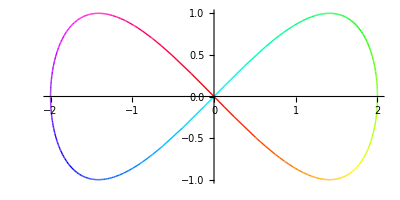

```mathematica
Subscript[curve, 0][u_]:={2Sin[u],-Sin[2u]};
ParametricPlot[Subscript[curve, 0][u],{u,0,4Pi/2},ColorFunction->Function[{x,y,u},Hue[u]]]
```

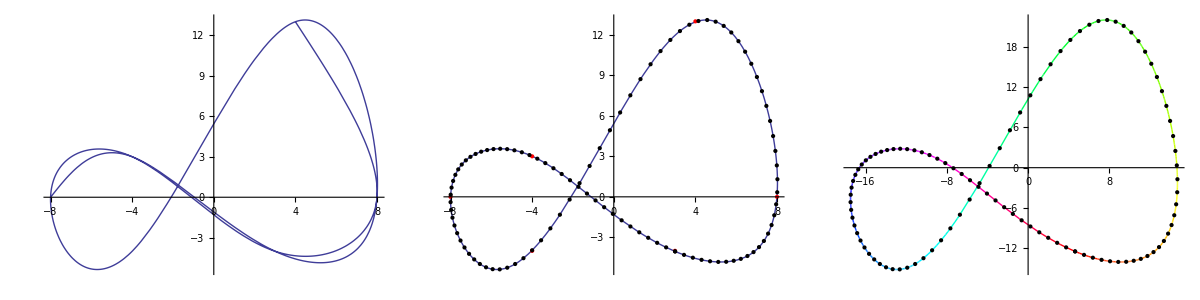

{-316.754,67.0864,{0.702376,2.15904}}

```mathematica
curgen[1,{{3,-4},{8,0},{4,13},{-4,-4},{-8,0},{-4,3}}]
```

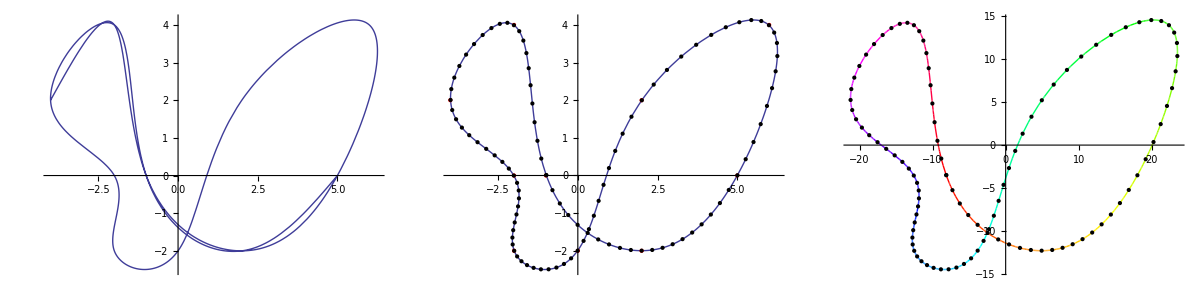

{-182.918,35.746,{0.872884,0.807773}}

```mathematica
curgen[2,{{-1,0},{2,-2},{5,0},{6,4},{2,2},{0,-2},{-2,-2},{-2,0},{-4,2},{-2,4}}]
```

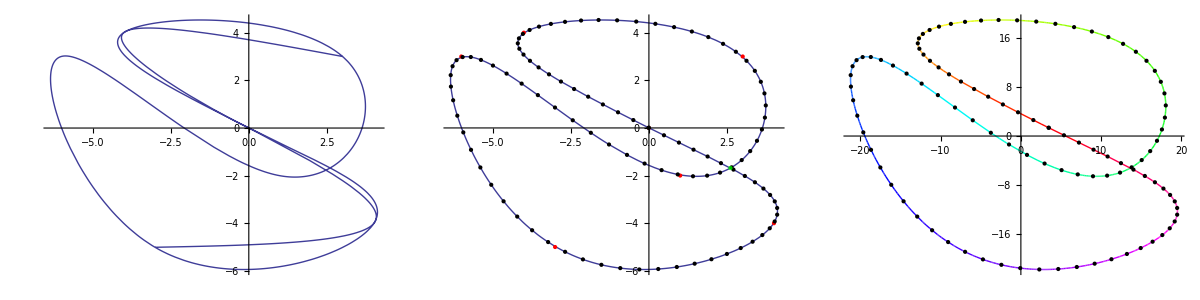

{-248.756,52.047,{-0.896688,-0.339774}}

```mathematica
curgen[3,{{0,0},{-4,4},{3,3},{1,-2},{-6,3},{-3,-5},{4,-4}},2.6]
```

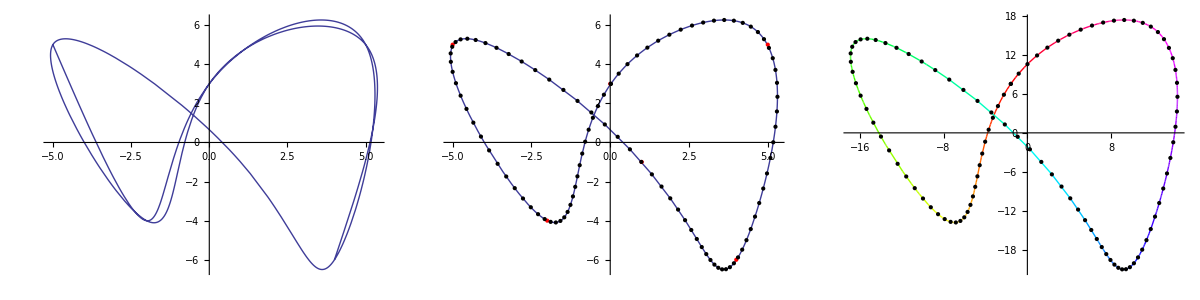

{-198.331,51.5239,{0.544023,0.488924}}

```mathematica
curgen[4,{{0,3},{-2,-4},{-5,5},{1,-1},{4,-6},{5,5}}]
```

### evolution & isofit

#### evolution

```mathematica
evolution[1]
```

t=0,  error=0.0002,  error derivative=0.0009

t=1,  error=0.4401,  error derivative=-0.5607

t=2,  error=0.9449,  error derivative=-0.4268

t=3,  error=1.2820,  error derivative=-0.2498

t=4,  error=1.4540,  error derivative=-0.1005

t=5,  error=1.4950,  error derivative=0.0127

t=6,  error=1.4390,  error derivative=0.0945

t=7,  error=1.3140,  error derivative=0.1515

t=8,  error=1.1430,  error derivative=0.1897

t=9,  error=0.9400,  error derivative=0.2139

t=10,  error=0.7193,  error derivative=0.2278

t=11,  error=0.4878,  error derivative=0.2341

t=12,  error=0.2528,  error derivative=0.2350

t=13,  error=0.0191,  error derivative=0.2319

t=14,  error=0.2099,  error derivative=0.2259

t=15,  error=0.4320,  error derivative=0.2180

t=16,  error=0.6452,  error derivative=0.2087

t=17,  error=0.8471,  error derivative=0.1986

t=18,  error=1.0390,  error derivative=0.1880

t=19,  error=1.2220,  error derivative=0.1772

t=20,  error=1.3940,  error derivative=0.1665

t=21,  error=1.5550,  error derivative=0.1562

t=22,  error=1.7060,  error derivative=0.1465

t=23,  error=1.8450,  error derivative=0.1380

t=24,  error=1.9790,  error derivative=0.1314

t=25, error tolerance exceeded: error=2.1080,  error derivative=0.1282

t=24., Fit: curve length dev: -0.00944298%. {da,dar,A0,dev da,dev dar} = {-316.808,-316.754,-316.754,-0.0169885,-4.44089×10^-14},  {0.339917,1.90234,108,92.4202}

t=26,  error=0.2511,  error derivative=0.0161

t=27,  error=0.2073,  error derivative=0.0783

t=28,  error=0.0779,  error derivative=0.1896

t=29,  error=0.1842,  error derivative=0.3319

t=30,  error=0.5161,  error derivative=0.2347

t=31, error tolerance exceeded: error=3.2040,  error derivative=33.6000

t=30., Fit: curve length dev: -0.430887%. {da,dar,A0,dev da,dev dar} = {-316.923,-316.754,-316.754,-0.0533479,2.22045×10^-14},  {0.594637,0.989614,96,78.0437}

t=31., Abort: error tolerance exceeded after fit,  error = 66.5504 (1.686,  error derivative = 240.747 (-1.68513 )

$Aborted

```mathematica
evoplot3d[1,2,31]
```

-Graphics3D-

```mathematica
evolution[2]
```

t=0,  error=0.0029,  error derivative=-0.0018

t=1,  error=0.5100,  error derivative=0.5798

t=2,  error=0.9618,  error derivative=0.3122

t=3,  error=1.1420,  error derivative=0.0605

t=4,  error=1.1080,  error derivative=-0.1154

t=5,  error=0.9333,  error derivative=-0.2244

t=6,  error=0.6756,  error derivative=-0.2839

t=7,  error=0.3770,  error derivative=-0.3096

t=8,  error=0.0645,  error derivative=-0.3131

t=9,  error=0.2445,  error derivative=-0.3029

t=10,  error=0.5392,  error derivative=-0.2850

t=11,  error=0.8143,  error derivative=-0.2633

t=12,  error=1.0670,  error derivative=-0.2408

t=13,  error=1.2970,  error derivative=-0.2194

t=14,  error=1.5080,  error derivative=-0.2005

t=15,  error=1.7010,  error derivative=-0.1849

t=16,  error=1.8820,  error derivative=-0.1732

t=17, error tolerance exceeded: error=2.0540,  error derivative=-0.1653

t=16., Fit: curve length dev: -0.0129726%. {da,dar,A0,dev da,dev dar} = {-182.973,-182.918,-182.918,-0.030265,-2.22045×10^-14},  {0.405096,1.66653,133,126.172}

t=18,  error=0.0557,  error derivative=0.3777

t=19,  error=0.4831,  error derivative=0.4685

t=20,  error=0.9780,  error derivative=0.5147

t=21,  error=1.5000,  error derivative=0.5250

t=22, error tolerance exceeded: error=2.0170,  error derivative=0.5029

t=21., Fit: curve length dev: -0.0724991%. {da,dar,A0,dev da,dev dar} = {-183.005,-182.918,-182.918,-0.0474168,-2.22045×10^-14},  {0.700964,1.08549,130,117.874}

t=23,  error=0.2713,  error derivative=0.1523

t=24,  error=0.0676,  error derivative=0.2510

t=25,  error=0.2219,  error derivative=0.3219

t=26,  error=0.5658,  error derivative=0.3587

t=27,  error=0.9277,  error derivative=0.3580

t=28,  error=1.2700,  error derivative=0.3201

t=29,  error=1.5580,  error derivative=0.2491

t=30,  error=1.7600,  error derivative=0.1522

t=31,  error=1.8560,  error derivative=0.0383

t=32,  error=1.8340,  error derivative=-0.0825

t=33,  error=1.6920,  error derivative=-0.2008

t=34,  error=1.4360,  error derivative=-0.3076

t=35,  error=1.0830,  error derivative=-0.3950

t=36,  error=0.6548,  error derivative=-0.4559

t=37,  error=0.1817,  error derivative=-0.4843

t=38,  error=0.3016,  error derivative=-0.4758

t=39,  error=0.7570,  error derivative=-0.4281

t=40,  error=1.1450,  error derivative=-0.3415

t=41,  error=1.4290,  error derivative=-0.2190

t=42,  error=1.5730,  error derivative=-0.0650

t=43,  error=1.5500,  error derivative=0.1179

t=44,  error=1.3260,  error derivative=0.3392

t=45,  error=0.8312,  error derivative=0.7041

t=46,  error=0.5656,  error derivative=3.0440

t=47, error tolerance exceeded: error=1844.0000,  error derivative=6447.0000

t=46., Fit: curve length dev: -0.202816%. {da,dar,A0,dev da,dev dar} = {-183.062,-182.918,-182.918,-0.0784364,-4.44089×10^-14},  {0.682765,0.96233,83,71.7275}

t=47., Abort: error tolerance exceeded after fit,  error = 26.2029 (3.4125,  error derivative = 45.0751 (-3.27653 )

$Aborted

```mathematica
evoplot3d[2,1,47]
```

-Graphics3D-

```mathematica
evolution[3]
```

t=0,  error=0.0006,  error derivative=0.0075

t=1, error tolerance exceeded: error=3.4220,  error derivative=-3.8360

t=0., Fit: curve length dev: -0.508287%. {da,dar,A0,dev da,dev dar} = {-248.989,-248.756,-248.756,-0.0937775,-2.22045×10^-14},  {0.438449,2.09462,150,202.734}

t=2, error tolerance exceeded: error=3.9920,  error derivative=-2.6330

t=1., Fit: curve length dev: -0.294336%. {da,dar,A0,dev da,dev dar} = {-248.967,-248.756,-248.756,-0.085191,-2.22045×10^-14},  {0.761471,1.6171,150,199.832}

t=3,  error=1.0800,  error derivative=-1.0240

t=4, error tolerance exceeded: error=2.1530,  error derivative=-1.1000

t=3., Fit: curve length dev: -0.150531%. {da,dar,A0,dev da,dev dar} = {-248.906,-248.756,-248.756,-0.0604288,-8.88178×10^-14},  {0.85142,1.47943,150,195.796}

t=5,  error=0.2040,  error derivative=-0.3762

t=6,  error=0.6221,  error derivative=-0.4519

t=7,  error=1.0950,  error derivative=-0.4879

t=8,  error=1.5890,  error derivative=-0.4972

t=9, error tolerance exceeded: error=2.0830,  error derivative=-0.4878

t=8., Fit: curve length dev: -0.0486819%. {da,dar,A0,dev da,dev dar} = {-248.534,-248.756,-248.756,0.0890891,-2.22045×10^-14},  {0.894231,1.41349,148,187.364}

t=10,  error=0.0306,  error derivative=-0.1280

t=11,  error=0.1184,  error derivative=-0.1674

t=12,  error=0.2997,  error derivative=-0.1933

t=13,  error=0.5017,  error derivative=-0.2094

t=14,  error=0.7160,  error derivative=-0.2180

t=15,  error=0.9357,  error derivative=-0.2204

t=16,  error=1.1550,  error derivative=-0.2178

t=17,  error=1.3700,  error derivative=-0.2110

t=18,  error=1.5760,  error derivative=-0.2008

t=19,  error=1.7710,  error derivative=-0.1877

t=20,  error=1.9510,  error derivative=-0.1722

t=21, error tolerance exceeded: error=2.1140,  error derivative=-0.1551

t=20., Fit: curve length dev: -0.0809067%. {da,dar,A0,dev da,dev dar} = {-248.805,-248.756,-248.756,-0.0200135,4.44089×10^-14},  {0.907741,1.33791,140,169.063}

t=22,  error=0.0289,  error derivative=-0.0628

t=23,  error=0.0448,  error derivative=-0.0832

t=24,  error=0.1354,  error derivative=-0.0970

t=25,  error=0.2373,  error derivative=-0.1060

t=26,  error=0.3461,  error derivative=-0.1112

t=27,  error=0.4586,  error derivative=-0.1133

t=28,  error=0.5719,  error derivative=-0.1130

t=29,  error=0.6839,  error derivative=-0.1107

t=30,  error=0.7928,  error derivative=-0.1068

t=31,  error=0.8970,  error derivative=-0.1015

t=32,  error=0.9954,  error derivative=-0.0952

t=33,  error=1.0870,  error derivative=-0.0881

t=34,  error=1.1710,  error derivative=-0.0804

t=35,  error=1.2480,  error derivative=-0.0724

t=36,  error=1.3160,  error derivative=-0.0642

t=37,  error=1.3760,  error derivative=-0.0560

t=38,  error=1.4280,  error derivative=-0.0479

t=39,  error=1.4720,  error derivative=-0.0400

t=40,  error=1.5080,  error derivative=-0.0324

t=41,  error=1.5370,  error derivative=-0.0252

t=42,  error=1.5590,  error derivative=-0.0183

t=43,  error=1.5740,  error derivative=-0.0120

t=44,  error=1.5830,  error derivative=-0.0061

t=45,  error=1.5860,  error derivative=-0.0008

t=46,  error=1.5850,  error derivative=0.0041

t=47,  error=1.5780,  error derivative=0.0084

t=48,  error=1.5680,  error derivative=0.0122

t=49,  error=1.5540,  error derivative=0.0155

t=50,  error=1.5370,  error derivative=0.0183

t=51,  error=1.5180,  error derivative=0.0206

t=52,  error=1.4960,  error derivative=0.0226

t=53,  error=1.4730,  error derivative=0.0241

t=54,  error=1.4480,  error derivative=0.0252

t=55,  error=1.4230,  error derivative=0.0259

t=56,  error=1.3970,  error derivative=0.0264

t=57,  error=1.3700,  error derivative=0.0265

t=58,  error=1.3430,  error derivative=0.0264

t=59,  error=1.3170,  error derivative=0.0261

t=60,  error=1.2910,  error derivative=0.0256

t=61,  error=1.2660,  error derivative=0.0249

t=62,  error=1.2420,  error derivative=0.0240

t=63,  error=1.2180,  error derivative=0.0230

t=64,  error=1.1960,  error derivative=0.0220

t=65,  error=1.1740,  error derivative=0.0208

t=66,  error=1.1540,  error derivative=0.0196

t=67,  error=1.1350,  error derivative=0.0184

t=68,  error=1.1170,  error derivative=0.0170

t=69,  error=1.1010,  error derivative=0.0156

t=70,  error=1.0860,  error derivative=0.0142

t=71,  error=1.0730,  error derivative=0.0127

t=72,  error=1.0610,  error derivative=0.0110

t=73,  error=1.0510,  error derivative=0.0093

t=74,  error=1.0420,  error derivative=0.0074

t=75,  error=1.0360,  error derivative=0.0053

t=76,  error=1.0320,  error derivative=0.0031

t=77,  error=1.0330,  error derivative=0.0007

t=78,  error=1.0340,  error derivative=-0.0018

t=79,  error=1.0380,  error derivative=-0.0039

t=80,  error=1.0440,  error derivative=-0.0046

t=81,  error=1.0510,  error derivative=-0.0005

t=82,  error=1.0490,  error derivative=0.0242

t=83,  error=0.9595,  error derivative=0.2704

t=84, error tolerance exceeded: error=386.0000,  error derivative=4852.0000

t=83., Fit: curve length dev: -0.210548%. {da,dar,A0,dev da,dev dar} = {-248.82,-248.756,-248.756,-0.0260577,1.11022×10^-14},  {0.891283,1.28209,60,68.529}

t=84., Abort: error tolerance exceeded after fit,  error = 235.045 (17.7302,  error derivative = 2188.44 (-23.8107 )

$Aborted

```mathematica
evoplot3d[3,2,84]
```

-Graphics3D-

#### error considerations

```mathematica
Plot[{length[Subscript[solution, 1][[1]],t],D[length[Subscript[solution, 1][[1]],tt], tt]/.tt->t},{t,0,25},PerformanceGoal->"Speed"]
```

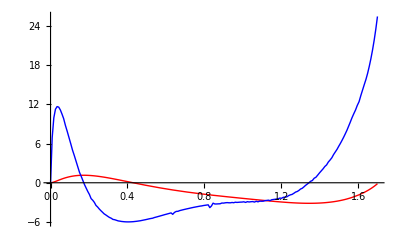

```mathematica
Plot[{(1-areadiff[Subscript[solution, 2],t]/Subscript[A0, 2])10^6,(-(D[areadiff[Subscript[solution, 2],tt], tt])/.tt->t)/Subscript[A0, 2]10^6},{t,0,1.7},PerformanceGoal->"Speed",MaxRecursion->1,PlotRange->All,PlotStyle->{Red,Blue}]
```

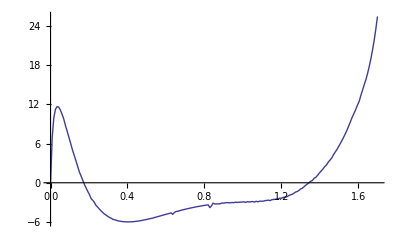

```mathematica
Plot[{(-(D[areadiff[Subscript[solution, 2],tt], tt])/.tt->t)/Subscript[A0, 2]10^6},{t,0,1.7},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
Timing[(D[areadiff[Subscript[solution, 2][[1]],t], t])/.t->2]
```

{0.200013,0.0000571058}

```mathematica
Timing@Block[{sol=Subscript[solution, 2],tval=2,t,n,grid,X,Y,Xt,Yt,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][tval]]/.sol;
Y=Through[Thread[Subscript[y, grid]][tval]]/.sol;
Xt=D[(Through[Thread[Subscript[x, grid]][t]]/.sol), t]/.t->tval;
Yt=D[(Through[Thread[Subscript[x, grid]][t]]/.sol), t]/.t->tval;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Print[fddf[Xt]];

Total[Drop[Yt fddf[X]+Y fddf[Xt]Yt -Xt fddf[Y]-X fddf[Yt],1]]/2

]
```

### intersection

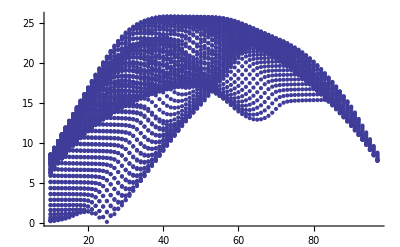

```mathematica
distdistplot[1,31]
```

{{60,142},{{13.3357,-5.44662},{14.0259,-5.49233}}}

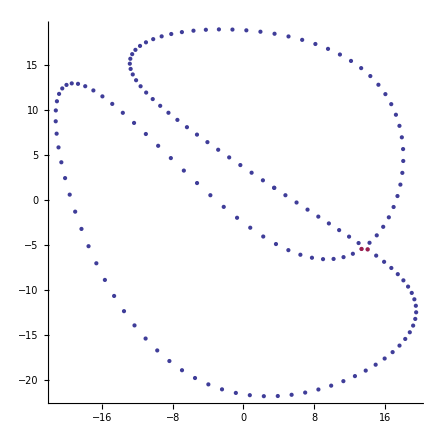

```mathematica
Block[{t=0,num=3,sol,i1,i2,p1,p2},
sol=Subscript[solution, num];
{i1,i2}=intersection[sol,t];
p1=coordselect[sol,t][[{1,2},i1]];
p2=coordselect[sol,t][[{1,2},i2]];
Print[{{i1,i2},{p1,p2}}];
ListPlot[Table[{Subscript[x, i][t],Subscript[y, i][t]}/.sol[[1]],{i,0,150}],Epilog->{Red,Opacity[.5],PointSize[Medium],Point[{p1,p2}]},AspectRatio->Automatic]
]
```

```mathematica
farea[num_,t_]:=
Module[{sol,X,Y,n,dgrid,fddf,dist,ltotal,l,grid,xmdp,ymdp,order=16,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,fc,area},
sol=Subscript[solution, num];
{X,Y}=coordselect[sol,t];

n=Length[X]-1;
dgrid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], dgrid];

dist=Sqrt[fddf[X]^2 +fddf[Y]^2];
ltotal=Total[Drop[dist,1]];

Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+dist[[i]],{i,1,n}];

grid=Table[{2π Subscript[l, i]/ltotal,{X[[i]],Y[[i]]}},{i,1,n}];
grid=Prepend[grid,{0,Last[grid][[2]]}];

xmdp=Table[{grid[[i,1]],grid[[i,2,1]]},{i,1,n+1}];
ymdp=Table[{grid[[i,1]],grid[[i,2,2]]},{i,1,n+1}];

xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xmdp,xexp[u],xpara ,u];
yfitdat=FindFit[ymdp,yexp[u],ypara ,u];

fc[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

area=Block[{u1,u2,a1,a2},
{u1,u2}={u,p}/.FindRoot[{fc[u]==fc[p]},{{u,0π},{p,π}},MaxIterations->100];

a1=1/2NIntegrate[Evaluate[(fc[u][[2]])( D[fc[u][[1]], u])-(fc[u][[1]])(D[fc[u][[2]], u])],{u,u1,u2},AccuracyGoal->8];
a2=1/2NIntegrate[Evaluate[(fc[u][[2]])( D[fc[u][[1]], u])-(fc[u][[1]])(D[fc[u][[2]], u])],{u,u2,2π+u1},AccuracyGoal->8];

Abs[a1]+Abs[a2]
(*{u1,u2,a1,a2,Abs[Abs[a1]-Abs[a2]],Abs[a1]+Abs[a2]}*)

]
];
```